```mathematica
<<MaTeX`
```

```mathematica
magnif = 1.5;
markerLine = Graphics[{#, Rectangle[{0, 0}, {1, 0.1}]}]&;(* markers for plotting *)
markerCirc = Graphics[{#, EdgeForm[{#}], FaceForm[Opacity[.075]], Disk[]}]&;
markerDisk = Graphics[{#,  EdgeForm[{#}], FaceForm[Opacity[0.7]], Disk[]}]&;
markerTriangle[fillCol_, bondCol_]:=  Graphics[{fillCol,  EdgeForm[{bondCol}], FaceForm[Opacity[.7]], Triangle[{{0,0},{0.5, (√3)/2},{1,0}}]}];
(* markers examples *)
GraphicsRow[{ markerCirc[Gray],markerDisk[Gray], markerTriangle[Gray, Gray] }, ImageSize->100]
markerDiskWithBoundAndText[fillCol_, bondCol_, text_] := Graphics[{ fillCol,EdgeForm[{bondCol}], FaceForm[Opacity[0.3]], Disk[], Text[Style[MaTeX[text, Magnification->1], Black],{0,0}]}];
markerTriangleWithText[fillCol_, bondCol_,text_] :=  Graphics[{fillCol,  EdgeForm[{bondCol}], FaceForm[Opacity[.7]], Triangle[{{0,0},{0.5, (√3)/2},{1,0}}],Text[Style[MaTeX[text, Magnification->1], Black],{0.5,0.3}]}];
```

-Graphics-

### Training History

```mathematica
(* "Epoch","Loss","Val. Loss"*)
TrainingHistory=Import[NotebookDirectory[]<>"/eval_results/history_2000_epoch_50_estimators.csv", "Data"]⟦2;;⟧;
```

```mathematica
estimatorsHistory = Table[TrainingHistory⟦2000 (i-1)+1;; 2000 (i -  1)+ 2000⟧,{i, 50}];
```

```mathematica
averagedHistory = Total[estimatorsHistory⟦;;,;;, {2, 3}⟧] /50;
```

```mathematica
legendHistory = PointLegend[{Automatic,Automatic},MaTeX[#, Magnification->1.5]&/@{
"\\text{Training}",
"\\text{Validation}"
},
LegendMarkers->{
markerLine[RGBColor["#0079FF"]],
markerLine[RGBColor["#FC4F00"]]
}]
```

```mathematica
histLoss = Show[
ListLinePlot[averagedHistory⟦;;,1⟧,PlotRange->All, PlotStyle->RGBColor["#0079FF"]],
ListLinePlot[averagedHistory⟦;;,2⟧, PlotRange->All, PlotStyle->RGBColor["#FC4F00"]],

PlotRange->{{-50, 2000}, {-0.001, 0.05}},
FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\text{Epoch}", "\\text{MSE Loss}"},
FrameTicks->{
{Table[{x,MaTeX[x,Magnification->magnif]},
{x,{ 0, 0.025, 0.05}}],
None},
{Table[{x,MaTeX[x,Magnification->magnif]},
{x,{0,1000,2000}}],
None}},
Axes->False,
AspectRatio->1,
Frame->True,
PlotRangePadding->None
];
```

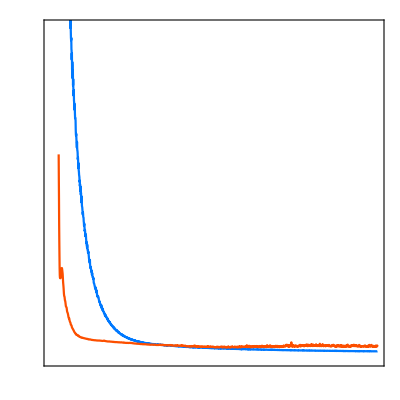

```mathematica
histLossLegend=Overlay[{legendHistory, histLoss}, Alignment->{0.6,0.6}]
```

```mathematica
Export[NotebookDirectory[]<>"/figs/hist_loss.svg", histLossLegend, ImageResolution->300,Background->None]
```

/Users/denyskononenko/Documents/ifw/smcp/backend/ml//figs/hist_loss.svg

### Model Performance

```mathematica
RSquared[yTrue_, yPred_]:=Module[{meanY, SSR, SST, Rs},
meanY=Mean[yTrue];
SSR = Total[Table[(yTrue⟦i⟧-yPred⟦i⟧)^2, {i ,Length@yPred}]];
SST = Total[Table[(yTrue⟦i⟧-meanY)^2, {i ,Length@yPred}]];
Rs = IntegerPart[(1 - SSR/SST)*100]/100//N;
Rs
]
```

```mathematica
data4plots = NotebookDirectory[]<>"eval_results/";
(* data with GPR evaluation *)
(* Y Y_pred *)
evalTrain =  Import[data4plots<>"random_split_100_estimators_08092023-15-02_train.csv", "Data"]⟦2;;⟧;(*ToExpression@(StringSplit@StringReplace[#,{"e+":>"*^","e-":>"*^-"}]&/@ReadList[data4plots<>"train_std_2023-03-16_14-59-32.dat", String]⟦2;;⟧)//N;*)
evalTest =Import[data4plots<>"random_split_100_estimators_08092023-15-02_test.csv", "Data"]⟦2;;⟧; (*ToExpression@(StringSplit@StringReplace[#,{"e+":>"*^","e-":>"*^-"}]&/@ReadList[data4plots<>"test_std_2023-03-16_14-59-32.dat", String]⟦2;;⟧)//N;*)
```

```mathematica
(* colors for markers *)
trainMCol =RGBColor["#0080FF"]; 
testMCol =RGBColor["#696969"];  (* color for markers of fit model evaluation *)
```

```mathematica
axTicks = {0,0.1, 0.2, 0.3, 0.4, 0.5, 0.6};
verticalSize = 400;
```

```mathematica
legendEval = PointLegend[{Automatic,Automatic},MaTeX[#, Magnification->1.5]&/@{"\\text{Training}", "\\text{Testing}"},LegendMarkers->{
markerDisk[trainMCol],
markerDisk[testMCol]
}]
```

```mathematica
Print["Train Data"]
Print["RMSE = "<>ToString@RootMeanSquare[evalTrain⟦;;, 1⟧-evalTrain⟦;;, 2⟧]]
Print["MAE = "<>ToString@Mean[Abs[evalTrain⟦;;, 1⟧-evalTrain⟦;;, 2⟧]]]
Print["R^2 = "<>ToString@RSquared[evalTrain⟦;;, 1⟧,evalTrain⟦;;, 2⟧]]
```

Train Data

RMSE = 0.0163924309196992001

MAE = 0.0113064264667698536

R^2 = 0.9

```mathematica
Print["Test Data"]
Print["RMSE = "<>ToString@RootMeanSquare[evalTest⟦;;, 1⟧-evalTest⟦;;, 2⟧]]
Print["MAE = "<>ToString@Mean[Abs[evalTest⟦;;, 1⟧-evalTest⟦;;, 2⟧]]]
Print["R^2 = "<>ToString@RSquared[evalTest⟦;;, 1⟧,evalTest⟦;;, 2⟧]]
```

Test Data

RMSE = 0.0276619616172633500

MAE = 0.0177594714550253221

R^2 = 0.7

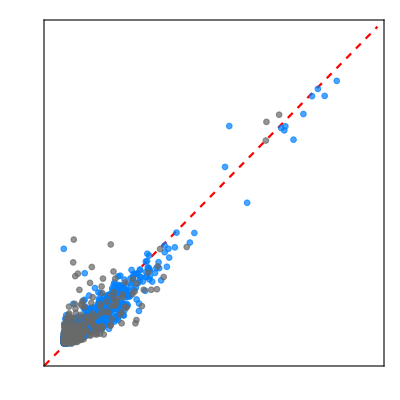

```mathematica
GPREvalPlot = Show[
(*SmoothDensityHistogram[evalRFRCorner, PlotRangePadding->None, PlotRange->All, ColorFunction->"LightTerrain"],*)
(*SmoothDensityHistogram[evalGPRTrain, PlotRangePadding->None,PlotRange->{{-0.05,0.6}, {-0.05, 0.6}}, ColorFunction->"LightTerrain"],*)
Plot[x, {x, -0.05, 0.6}, PlotStyle->{Dashed, Red}, PlotRange->All],
ListPlot[evalTrain⟦;;, {1, 2}⟧, PlotMarkers->{markerDisk[rfrMCol], 0.02}, PlotRange->All],
ListPlot[evalTest⟦;;, {1,2}⟧, PlotMarkers->{markerDisk[fitMCol], 0.02}, PlotRange->All],

PlotRange->{{-0.02,0.6}, {-0.02, 0.6}},
Frame->True,
FrameTicks->{{{#, MaTeX[#,Magnification->1.5]}&/@axTicks, None}, {{#, MaTeX[#,Magnification->1.5]}&/@axTicks, None}},
FrameLabel->{MaTeX["t_{ij}^{\\text{DFT}}, \\text{eV}", Magnification->1.5], MaTeX["t_{ij}^{\\text{prediction}}, \\text{eV}", Magnification->1.5],
None(*MaTeX["\\text{Corner-sharing}", Magnification->1.5]*)},
PlotRangePadding->None,
AspectRatio->1,
ImageSize->{Automatic,verticalSize}
]
```

```mathematica
GPREvalPlotWithLegend = Overlay[{legendEval, GPREvalPlot}, Alignment->{-0.5,0.8}]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"/figs/ann_eval_test_train.svg",GPREvalPlotWithLegend]
```

/Users/denyskononenko/Documents/ifw/smcp/backend/ml//figs/ann_eval_test_train.svg

```mathematica
Residuals = Table[evalTest⟦i, 1⟧ - evalTest⟦i, 2⟧, {i, 1, Length@evalTest}];
```

```mathematica
μ = (IntegerPart[Mean[Residuals] * 10^4]/10^4)//N;
σ = (IntegerPart[StandardDeviation[Residuals] * 10^3]/10^3)//N;
errorLabel = MaTeX["\\substack{\\sigma = "<>ToString[σ 10^3]<>"\,\\text{meV}"<> " \\\\ \\mu = " <>ToString[μ 10^3]<>"\,\\text{meV}"<>"}", Magnification->2]
```

-Graphics-

```mathematica
errorDistrib =Show[
 Histogram[Residuals,40, ChartStyle->EdgeForm[None], PlotRange->{{-0.2, 0.2}, {0,25}}],
Plot[PDF[NormalDistribution[μ,σ],x],{x, -0.2, 0.2}],

PlotRange->{{-0.2, 0.2}, {0,70}},
ImageSize->200,
Frame->True,
AspectRatio->0.8,
PlotRangePadding->None,
FrameLabel->(MaTeX[#, Magnification->1.5]&)/@{"t_{ij}^{\\text{DFT}} - t_{ij}^{\\text{prediction}}\\text{, eV}", "\\text{Count}"},
FrameTicks->{{ {# ,MaTeX[#, Magnification->1.5]}&/@{0, 20, 40, 60}, None}, 
{{# ,MaTeX[#, Magnification->1.5]}&/@{-0.2, -0.1, 0, 0.1, 0.2}, None}}
];
```

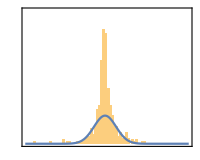
-Graphics--Graphics-

```mathematica
errorDistrbOverlay =Overlay[{
errorLabel,
errorDistrib},
Alignment->{1,1}
]
```

```mathematica
Export[NotebookDirectory[]<>"/figs/residuals.svg",errorDistrbOverlay]
```

/Users/denyskononenko/Documents/ifw/smcp/backend/ml//figs/residuals.svg

```mathematica
tijsvg = MaTeX["r_{ij}, \\AA", Magnification->1.5]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"/figs/auxtext.svg",tijsvg]
```

/Users/denyskononenko/Documents/ifw/smcp/backend/ml//figs/auxtext.svg

```mathematica
(50.14 + 73.18)/2
```

61.66

### Test on HTS Cuprates

```mathematica
(* { Cu-Apical oxygen distance, t'_DFT / t_DFT, t'_ML / t_ML } *)
La2CuO4 = {{2.39, 84.5 / 385.37,90.185 /381.78 }};(* batch0/34332 *)
LaBa2Cu3O7 = {{2.23, 0000}};

Bi2Sr2CuO6 = {{2.59, 105.055 / 397.61,107.455 / 403.55}}; (* batch2/67426 *)

HgBa2CuO4 = {{2.79,94.11/ 397.83,111 / 432(* 93.55 / 467.58*)}}; (* batch0/35943 *)
HgBa2CaCu2O6 = {{2.79, 69.44 / 395.6}};
HgBa2Ca2Cu3O8 = {{2.75, 61.66/ 425.41}};

Tl2Ba2CuO6 = {{2.699,104.13/385.89, 95.5 / 318.96}}; (* batch0/68582 *)
Tl2Ba2CaCu2O8 = {{2.697, 72.07 / 397.71}};
Tl2Ba2Ca2Cu3O10 = {{2.15, 73.83/ 391.88}};
```

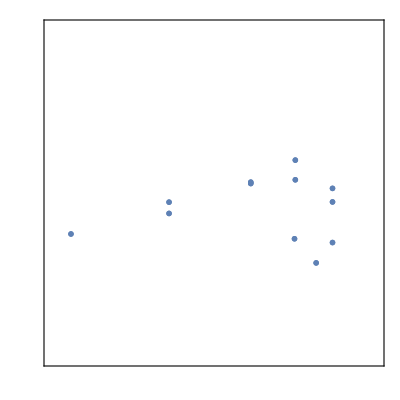

```mathematica
msize = 0.07;
(* 1-Tl2Ba2Ca2Cu3O10, 2-La2CuO4, 3-Bi2Sr2CuO6, 4-Tl2Ba2CuO6, 5-HgBa2CuO4, 6-Tl2Ba2CaCu2O8, 7-HgBa2CaCu2O6, 8-HgBa2Ca2Cu3O8 *)
HTCPlot = Show[
ListPlot[La2CuO4⟦;;,{1,2}⟧, PlotMarkers->{{markerTriangleWithText[White, Orange, "2"], msize}}],
ListPlot[La2CuO4⟦;;,{1,3}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black, "2"], msize}}],

ListPlot[Bi2Sr2CuO6⟦;;,{1,2}⟧, PlotMarkers->{{markerTriangleWithText[White, Orange, "3"], msize}}],
ListPlot[Bi2Sr2CuO6⟦;;,{1,3}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black, "3"], msize}}],

ListPlot[HgBa2CuO4⟦;;,{1,2}⟧, PlotMarkers->{{markerTriangleWithText[White, Orange, "5"], msize}}],
ListPlot[HgBa2CuO4⟦;;,{1,3}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black,"5"], msize}}],

ListPlot[Tl2Ba2CuO6⟦;;,{1,2}⟧, PlotMarkers->{{markerTriangleWithText[White, Orange, "4"], msize}}],
ListPlot[Tl2Ba2CuO6⟦;;,{1,3}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black,"4"],msize}}],

ListPlot[HgBa2CaCu2O6⟦;;,{1,2}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black, "7"],msize}}],
ListPlot[HgBa2Ca2Cu3O8⟦;;,{1,2}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black, "8"], msize}}],
ListPlot[Tl2Ba2CaCu2O8⟦;;,{1,2}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black,"6"],msize}}],
ListPlot[Tl2Ba2Ca2Cu3O10⟦;;,{1,2}⟧, PlotMarkers->{{markerDiskWithBoundAndText[White, Black, "1"], msize}}],


Frame->True,
AspectRatio->1,
PlotRange->{{2.1, 2.9}, {0, 0.5}},

FrameLabel->(MaTeX[#,Magnification->1.5]&)/@{"\\text{Cu-Apical Oxygen Distance }d_\\text{CAO}\\text{, \\r{A}}", "t_2/t_1"},
FrameTicks->{
{Table[{x,MaTeX[x,Magnification->magnif]},
{x,{0, 0.1, 0.2, 0.3, 0.4, 0.5}}],
None},
{Table[{x,MaTeX[x,Magnification->magnif]},
{x, { 2.2,  2.4,  2.6, 2.8, 3}}],
None}}
];
(* make legend *)
HTClegend= PointLegend[
{Automatic,Automatic},
MaTeX[#, Magnification->magnif]&/@{
"\\text{Prediction}",
"\\text{DFT}"
},
LegendMarkers->{
{markerDiskWithBound[White, Black],1.1 msize},
{markerTriangle[White, Orange], 1.1msize}
}];

HTCPlotWithLegend= Overlay[{HTCPlot, HTClegend}, Alignment->{-0.3, -0.4}]
```

```mathematica
Export[NotebookDirectory[]<>"/figs/hts_plot.svg", HTCPlotWithLegend]
```

/Users/denyskononenko/Documents/ifw/smcp/backend/ml//figs/hts_plot.svg

```mathematica
descrText = MaTeX["\\text{La},\\text{Bi},\\text{Tl},\\text{Hg}, d_\\text{CAO}, \\text{\\r{A}},\\text{Cu}, \\text{O}, t_1, t_2", Magnification->magnif]
```

-Graphics-

```mathematica
Export[NotebookDirectory[]<>"/figs/aux_text.svg", descrText]
```

/Users/denyskononenko/Documents/ifw/smcp/backend/ml//figs/aux_text.svg

### HTSC Structure Plot

```mathematica
t2Col = RGBColor@"#F94C10";
t1Col = RGBColor@"#C70039";
CuColor = RGBColor@"#102C57";
CuRad = 0.15;
OxColor = RGBColor@"#DAC0A3";
OxRad = 0.08;
Sp1Rad = 0.3;
Sp1Col = RGBColor@"#A8A196";

MakeTube[p1_, p2_, color_, rad_]:=Graphics3D[{color, Tube[{p1,  p2}, rad]}];
MakeDoubleTube[p1_, p2_, color1_, color2_, rad_, opacity_:1.0]:={Graphics3D[{color1,Opacity[opacity], Tube[{p1,  (p2 + p1)/2}, rad]}],Graphics3D[{color2,Opacity[opacity], Tube[{(p2 + p1)/2,  p2}, rad]}]}
MakeDoubleArrow[p1_, p2_, color_, rad_, head_]:=Graphics3D[{color, Arrowheads[{-head, head}],Arrow[Tube[{p1,p2}, rad]]}]
```

```mathematica
htct1t2Plot =Show[{
(* Cu atoms *)
Graphics3D[{CuColor, Sphere[{0,0,0.5}, CuRad]}],
Graphics3D[{CuColor, Sphere[{1,0,0.5}, CuRad]}],
Graphics3D[{CuColor, Sphere[{1,1,0.5}, CuRad]}],
Graphics3D[{CuColor, Sphere[{0,1,0.5}, CuRad]}],
(* apical oxygen *)
Graphics3D[{OxColor, Sphere[{0,0,1}, OxRad]}],
Graphics3D[{OxColor, Sphere[{1,0,1}, OxRad]}],
Graphics3D[{OxColor, Sphere[{1,1,1}, OxRad]}],
Graphics3D[{OxColor, Sphere[{0,1,1}, OxRad]}],
Graphics3D[{OxColor, Sphere[{0,0,0}, OxRad]}],
Graphics3D[{OxColor, Sphere[{1,0,0}, OxRad]}],
Graphics3D[{OxColor, Sphere[{1,1,0}, OxRad]}],
Graphics3D[{OxColor, Sphere[{0,1,0}, OxRad]}],
(* Oxygen plaquete *)
Graphics3D[{OxColor, Sphere[{-0.5,0,0.5}, OxRad]}],
Graphics3D[{OxColor, Sphere[{0.5,0,0.5}, OxRad]}],
Graphics3D[{OxColor, Sphere[{1.5,1,0.5}, OxRad]}],
Graphics3D[{OxColor, Sphere[{0,-0.5,0.5}, OxRad]}],
Graphics3D[{OxColor, Sphere[{1.0,-0.5,0.5}, OxRad]}],
Graphics3D[{OxColor, Sphere[{1.5,0,0.5}, OxRad]}],
Graphics3D[{OxColor, Sphere[{1.0,0.5,0.5}, OxRad]}],
Graphics3D[{OxColor, Sphere[{0,0.5,0.5}, OxRad]}],
Graphics3D[{OxColor, Sphere[{0.5,1.0,0.5}, OxRad]}],
Graphics3D[{OxColor, Sphere[{-0.5,1.0,0.5}, OxRad]}],
Graphics3D[{OxColor, Sphere[{0,1.5,0.5}, OxRad]}],
Graphics3D[{OxColor, Sphere[{1.0,1.5,0.5}, OxRad]}],
(* make bonds *)
MakeDoubleTube[{0,0,0.5}, {0,0,1}, CuColor, OxColor, 0.025],
MakeDoubleTube[{1,0,0.5}, {1,0,1}, CuColor, OxColor, 0.025],
MakeDoubleTube[{1,1,0.5}, {1,1,1}, CuColor, OxColor, 0.025],
MakeDoubleTube[{0,1,0.5}, {0,1,1}, CuColor, OxColor, 0.025],
MakeDoubleTube[{0,0,0.5}, {0,0,0}, CuColor, OxColor, 0.025],
MakeDoubleTube[{1,0,0.5}, {1,0,0}, CuColor, OxColor, 0.025],
MakeDoubleTube[{1,1,0.5}, {1,1,0}, CuColor, OxColor, 0.025],
MakeDoubleTube[{0,1,0.5}, {0,1,0}, CuColor, OxColor, 0.025],

MakeDoubleTube[{0,0,0.5}, {-0.5,0,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{0,0,0.5}, {0.5,0,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{0,0,0.5}, {0,-0.5,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{0,0,0.5}, {0,0.5,0.5}, CuColor, OxColor, 0.025],

MakeDoubleTube[{1,0,0.5}, {1,-0.5,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{1,0,0.5}, {0.5,0,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{1,0,0.5}, {1,0.5,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{1,0,0.5}, {1.5,0,0.5}, CuColor, OxColor, 0.025],

MakeDoubleTube[{1,1,0.5}, {1,0.5,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{1,1,0.5}, {1.5,1.0,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{1,1,0.5}, {1,1.5,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{1,1,0.5}, {0.5,1.0,0.5}, CuColor, OxColor, 0.025],

MakeDoubleTube[{0,1,0.5}, {0,0.5,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{0,1,0.5}, {-0.5,1.0,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{0,1,0.5}, {0,1.5,0.5}, CuColor, OxColor, 0.025],
MakeDoubleTube[{0,1,0.5}, {0.5,1.0,0.5}, CuColor, OxColor, 0.025],

(*MakeTube[{0,0,0.5},{0,0,0.75}, Blue, 0.025],
MakeTube[{0,0,0.75},{0,0,1}, Red, 0.025],*)
(*MakeTube[{1,0,0.5},{1,0,0.75}, Blue, 0.025],
MakeTube[{1,0,0.75},{1,0,1}, Red, 0.025],
MakeTube[{1,1,0.5},{1,1,0.75}, Blue, 0.025],
MakeTube[{1,1,0.75},{1,1,1}, Red, 0.025],
MakeTube[{0,1,0.5},{0,1,0.75}, Blue, 0.025],
MakeTube[{0,1,0.75},{0,1,1}, Red, 0.025],*)

(* tij *)
MakeTube[{0,0,0.5},{1,1,0.5}, t2Col, 0.04],
MakeTube[{0,1,0.5},{1,0,0.5}, t2Col, 0.04],

MakeTube[{0,0,0.5},{0,1,0.5}, t1Col, 0.04],
MakeTube[{0,1,0.5},{1,1,0.5}, t1Col, 0.04],
MakeTube[{1,1,0.5},{1,0,0.5}, t1Col, 0.04],
MakeTube[{0,0,0.5},{1,0,0.5}, t1Col, 0.04],

(* arrow *)
MakeDoubleArrow[{-0.25,-0.25,0.5}, {-0.25,-0.25,1}, Black, 0.01, 0.04],
(*MakeTube[{0,0,0.5},{-0.25,-0.25,0.5}, Black, 0.01],*)
MakeTube[{0,0,0.5},{-0.05,-0.05,0.5}, Black, 0.01],
MakeTube[{-0.1,-0.1,0.5},{-0.15,-0.15,0.5}, Black, 0.01],
MakeTube[{-0.2,-0.2,0.5},{-0.25,-0.25,0.5}, Black, 0.01],

(*MakeTube[{0,0,1},{-0.25,-0.25,1}, Black, 0.01]*)
MakeTube[{0,0,1},{-0.05,-0.05,1}, Black, 0.01],
MakeTube[{-0.1,-0.1,1},{-0.15,-0.15,1}, Black, 0.01],
MakeTube[{-0.2,-0.2,1},{-0.25,-0.25,1}, Black, 0.01],

(* Spacer *)
Graphics3D[{Sp1Col, Sphere[{0.5,0.5,1.8}, Sp1Rad]}],
Graphics3D[{Sp1Col, Sphere[{0.5,0.5,-1.3}, Sp1Rad]}],

MakeDoubleTube[{0.5,0.5,1.8}, {0.5,0,0.5}, Sp1Col, OxColor, 0.025, 0.3],
MakeDoubleTube[{0.5,0.5,1.8}, {0.5,1.0,0.5}, Sp1Col, OxColor, 0.025, 0.3],
MakeDoubleTube[{0.5,0.5,1.8}, {1.0,0.5,0.5}, Sp1Col, OxColor, 0.025, 0.3],
MakeDoubleTube[{0.5,0.5,1.8}, {0.0,0.5,0.5}, Sp1Col, OxColor, 0.025, 0.3],

MakeDoubleTube[{0.5,0.5,-1.3}, {0.5,0,0.5}, Sp1Col, OxColor, 0.025, 0.3],
MakeDoubleTube[{0.5,0.5,-1.3}, {0.5,1.0,0.5}, Sp1Col, OxColor, 0.025, 0.3],
MakeDoubleTube[{0.5,0.5,-1.3}, {1.0,0.5,0.5}, Sp1Col, OxColor, 0.025, 0.3],
MakeDoubleTube[{0.5,0.5,-1.3}, {0.0,0.5,0.5}, Sp1Col, OxColor, 0.025, 0.3]
},
(*Lighting-> {"Ambient", White},*)
Boxed->False,
ViewAngle->Automatic,ViewCenter->{0.5,0.5,0.5},ViewMatrix->Automatic,ViewPoint->{0.9764181163366074,-2.838267651477433,1.562320197868043},ViewProjection->Automatic,ViewRange->All,ViewVector->Automatic,ViewVertical->{0.15119938422701637,-0.40964807543460596,0.8996261448524573}]
```

-Graphics3D-

```mathematica
Export[NotebookDirectory[]<>"/figs/t1t2plaq.png", htct1t2Plot, ImageResolution->350, Background->None]
```

/Users/denyskononenko/Documents/ifw/smcp/backend/ml//figs/t1t2plaq.png